## set options

```mathematica
(* set working directory *)
SetDirectory[FileNameJoin[{$HomeDirectory,"phase_calculations"}]];
(* Plot and ListPlot options *)
SetOptions[Plot,Frame->True,PlotStyle->{Red,Green,Blue,Black}];
SetOptions[ListPlot,Frame->True,PlotStyle->{Red,Green,Blue,Black}];
```

## refractive index, vectors, ...

```mathematica
(* extraordinary refractive index in uniaxial crystals *)
nth[no_,ne_,θ_]:=no*ne/Sqrt[ne^2*Cos[θ]^2+no^2*Sin[θ]^2]
```

```mathematica
(* unit vector 
θ: polar angle ϕ: azimuthal angle *)
vect[Θ_,ϕ_]:={Sin[Θ]*Cos[ϕ],Sin[Θ]*Sin[ϕ],Cos[Θ]};
(* wave vector 
λ: wavelength in vacuum, nbr: refractive index, s: direction *)
kvect[λ_,nbr_,s__]:=2*π*nbr/λ*Normalize[s];
(* wave vector 
λ: wavelength in vacuum, nbr: refractive index, θ: polar angle ϕ: azimuthal angle *)
kvect[λ_,nbr_,Θ_,ϕ_]:=kvect[λ,nbr,vect[Θ,ϕ]];
```

```mathematica
(* Length of a crystal at Temperature T, L0 at 20°C *)
LT[L0_,α_,T_]:= L0+L0*(T-20)*α;
(* YVO4: α= 11.3 , see YVO4_temperature_12082015.nb *)
(* BBO: αa = 4*10^-6/K, αc=36*10^-6/K, Foctek homepage *)
```

## Sellmeier Equations

### YVO4

```mathematica
(*Sellmeier equations of Yttrium Vanadate crystals, Handbook of nonlinear optical crystals *)
(* http://www.redoptronics.com/Nd-YVO4-crystal.html 
http://www.foctek.net/products/YVO4.htm
thermal expansion: aa=4.43x10-6/K,ac=11.37x10-6/K
*)
(* wavelength in µm *)
nYVO[lambda_,temp_,axis:(e|o)]:=Module[{nr,x},
nr=If[MatchQ[axis,o],
Sqrt[(3.77834+0.069736/(lambda^2-0.04724)-0.0108133*lambda^2)]*(1+(temp-20)*8.5*10^-6),
Sqrt[4.59905+0.110534/(lambda^2-0.04813)-0.0122676*lambda^2]*(1+(temp-20)*3.0*10^-6)];
Return[nr]];
(*Refractive index of the extraordinary wave as a function of the polar angle (α) between optic axis and k vector *)
nYVOeo[λ_,temp_,α_]:=nth[nYVO[λ,temp,o],nYVO[λ,temp,e],α];
```

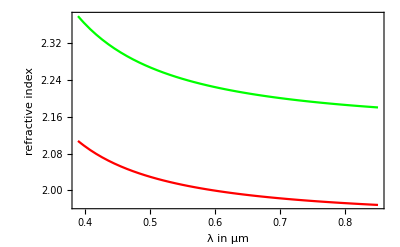

```mathematica
Plot[{nYVO[lam,20,o],nYVO[lam,20,e]},{lam,.39,.85},FrameLabel->{"λ in μm","refractive index"}]
```

### BBO

```mathematica
(* Sellmeier equations, BBO crystal *)
(* wavelength in µm *)
nBBO[lambda_,temp_,axis:(e|o)]:=Module[{nq,x},
nq=If[MatchQ[axis,o],
2.7359+0.01878/(lambda^2-0.01822)-0.01354*lambda^2,
2.3753+0.01224/(lambda^2-0.01667)-0.01516*lambda^2];
Sqrt[nq]+(InterpolatingPolynomial[If[MatchQ[axis,o],{{1.014,-16.64},{.579,-16.35},{.4047,-16.83}},{{1.014,-9.76},{.5790,-9.42},{.4047,-8.84}}],x]//.x->lambda)*10^-6*(temp-20)]
(*Refractive index of the extraordinary wave as a function of the polar angle (α) between optic axis and k vector*)
nBBOeo[λ_,temp_,θ_]:=nth[nBBO[λ,temp,o],nBBO[λ,temp,e],θ];
```

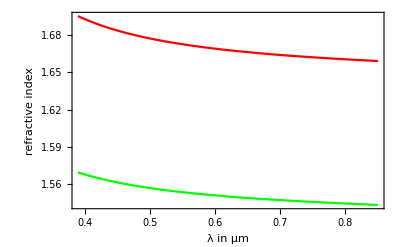

```mathematica
Plot[{nBBO[lam,20,o],nBBO[lam,20,e]},{lam,.39,.85},FrameLabel->{"λ in μm","refractive index"}]
```

## phase calculation

### - two BBO crystals (SPDC) - two YVO4 compensation crystals -Graphics-

the relative phase between HH and VV is calculated:
   |HH> + Exp[I*ϕ] |VV>

HH are generated in first BBO crystal

BBOs:
first BBO crystal: H:ordinary, V:extraordinary
second BBO crystal: V:ordinary, H:extraordinary
HH: extra-ordinary in second BBO crystal
VV: pump beam ordinary in first BBO crystal
exp(i*(kse+kie)L)|HH> + exp(i*kpo*L) |VV>
same quantum state: |HH> + exp(i*(kpo-kse-kie))*L ) |VV>

### phase difference in BBO crystals

```mathematica
Δdc = (kpo-(kse+kie))LBBO
```

(-kie+kpo-kse) LBBO

### phase difference in pre-compensation crystal

H: ordinary ,V: extraordinary
exp(i*kpeYVO*Lpc)|HH> + exp(i*kpoYVO*Lpc)*exp(i*Δdc ) |VV>

```mathematica
Δpc = (kpoYVO-kpeYVO4)*Lpc
```

(-kpeYVO4+kpoYVO) Lpc

### phase difference in compensation crystal

H(signal) and H(idler) ordinary
V(signal) and V(idler) extraordinary
exp(i*(ksoYVO+kioYVO)*Lc)|HH> + exp(i*(kseYVO+kieYVO)*Lc)*exp(i*(Δdc+Δpc ) |VV>

```mathematica
Δc = (kseYVO+kieYVO-(ksoYVO+kioYVO))*Lc
```

(kieYVO-kioYVO+kseYVO-ksoYVO) Lc

### phase behind all crystals, dc crystal and compensation with different length and material HH> + exp(i*(Δdc+Δpc +Δc)) |VV>

```mathematica
Δpc + Δdc + Δc
```

(-kie+kpo-kse) LBBO+(kieYVO-kioYVO+kseYVO-ksoYVO) Lc+(-kpeYVO4+kpoYVO) Lpc

```mathematica
pckvect = {kpeYVO4-> 2*π*nYVO[λp,Tpc,e]/λp,kpoYVO-> 2*π*nYVO[λp,Tpc,o]/λp};
ckvect =  {ksoYVO->2*π*nYVO[λs,Tc,o]/λs,kseYVO->2*π*nYVO[λs,Tc,e]/λs,kioYVO->2*π*nYVO[λi,Tc,o]/λi,kieYVO->2*π*nYVO[λi,Tc,e]/λi};
dckvect ={kpo-> 2*π*nBBO[λp,TBBO,o]/λp,kse->2*π*nBBOeo[λs,TBBO,θp]/λs,kie->2*π*nBBOeo[λi,TBBO,θp]/λi};
```

```mathematica
ϕdc[θp_,λp_,λs_,λi_,LBBO_,Lc_,Lpc_,TBBO_,Tc_,Tpc_]:=Evaluate[(Δpc +Δdc + Δc/. pckvect /.dckvect /.ckvect)];
ϕdc[θp_,λp_,λs_,LBBO_,Lc_,Lpc_,TBBO_,Tc_,Tpc_]:=ϕdc[θp,λp,λs,(1/λp-1/λs)^(-1),LBBO,Lc,Lpc,TBBO,Tc,Tpc]
```

## phase compensation calculations

```mathematica
sourceparameters = {L-> 6000.,Lc-> 3120.,Lpc->3440.,TBBO->20,Tc->20,Tpc->20,λp->0.406,λs->.765,Tbbo->20,ϕp->π/2,θp->0.5026584054092709}
```

{L→6000.,Lc→3120.,Lpc→3440.,TBBO→20,Tc→20,Tpc→20,λp→0.406,λs→0.765,Tbbo→20,ϕp→π/2,θp→0.502658}

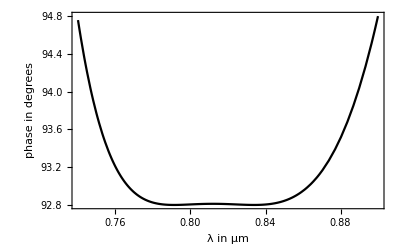

```mathematica
(* λs *)
Plot[Mod[180/π(ϕdc[θp,λp,λS,L,Lc,Lpc,TBBO,Tc,Tpc])/.sourceparameters,360],{λS,.740,.9},FrameLabel->{ "λ in µm","phase in degrees"},ImageSize->400,PlotRange->All]
```

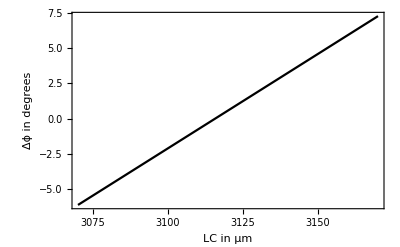

```mathematica
(* compensation crystal length, Δλs = 20 nm *)Plot[180/π(ϕdc[θp,λp,λs-.01,L,LC,Lpc,TBBO,Tc,Tpc]-ϕdc[θp,λp,λs+.01,L,LC,Lpc,TBBO,Tc,Tpc])/.sourceparameters,{LC,3070,3170},FrameLabel->{ "LC in µm","Δϕ in degrees"},ImageSize->400,PlotRange->All]
```

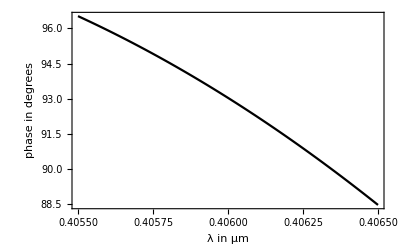

```mathematica
(* change of λp *)
Plot[Mod[180/π(ϕdc[θp,λP,λs,L,Lc,Lpc,TBBO,Tc,Tpc])/.sourceparameters,360],{λP,.4055,.4065},FrameLabel->{ "λ in µm","phase in degrees"},ImageSize->400,PlotRange->All]
```

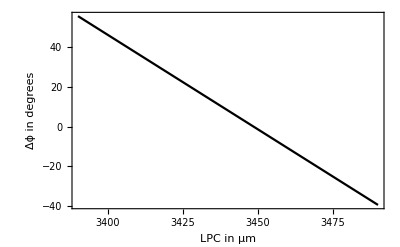

```mathematica
(* pre-compensation crystal length, Δλp = 1 nm *)Plot[180/π(ϕdc[θp,λp-0.0005,λs,L,Lc,LPC,TBBO,Tc,Tpc]-ϕdc[θp,λp+0.0005,λs,L,Lc,LPC,TBBO,Tc,Tpc])/.sourceparameters,{LPC,3390,3490},FrameLabel->{ "LPC in µm","Δϕ in degrees"},ImageSize->400,PlotRange->All]
```

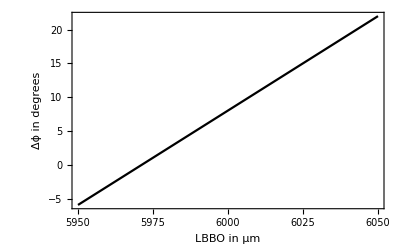

```mathematica
(* BBO crystal length, Δλp = 1 nm *)Plot[180/π(ϕdc[θp,λp-0.0005,λs,LBBO,Lc,Lpc,TBBO,Tc,Tpc]-ϕdc[θp,λp+0.0005,λs,LBBO,Lc,Lpc,TBBO,Tc,Tpc])/.sourceparameters,{LBBO,5950,6050},FrameLabel->{ "LBBO in µm","Δϕ in degrees"},ImageSize->400,PlotRange->All]
```

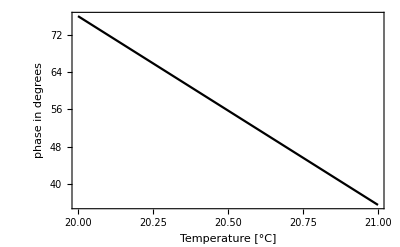

```mathematica
(* Temperature change, no pre-compensation YVO4 *)
Plot[Mod[180/π(ϕdc[θp,λp,λs,L,Lc,0*Lpc,T,T,T])/.sourceparameters,360],{T,20,21},FrameLabel->{ "Temperature [°C]","phase in degrees"},ImageSize->400,PlotRange->All]
```

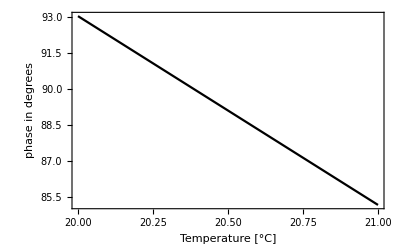

```mathematica
(* Temperature change, with pre-compensation YVO4 *)
Plot[Mod[180/π(ϕdc[θp,λp,λs,L,Lc,Lpc,T,T,T])/.sourceparameters,360],{T,20,21},FrameLabel->{ "Temperature [°C]","phase in degrees"},ImageSize->400,PlotRange->All]
```